# LAB 3

1) Rozwiązać równanie różniczkowe zupełne analitycznie oraz przy pomocy programu Mathematica.
(5x+4y) dx + (4x+8y^3) dy = 0

```mathematica
DSolve[{D[f[x,y],x]==5x+4y,D[f[x,y],y]==4-8y^3}, f, {x,y}]
```

DSolve[{f^(1,0)[x,y]==5 x+4 y,f^(0,1)[x,y]==4-8 y^3},f,{x,y}]

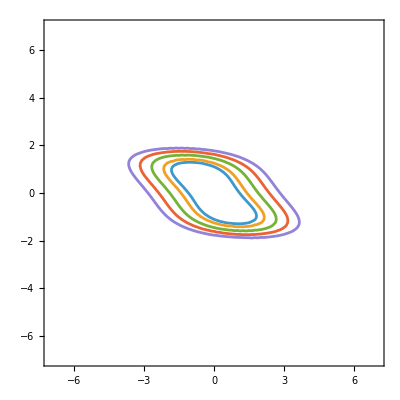

```mathematica
ContourPlot[{5/2*x^2+4*x*y+2*y^4==3,
5/2*x^2+4*x*y+2*y^4==5,
5/2*x^2+4*x*y+2*y^4==9,
5/2*x^2+4*x*y+2*y^4==14,
5/2*x^2+4*x*y+2*y^4==20},{x,-7,7},{y,-7,7}]
```

```mathematica
DSolve[5*x+4*y[x]+(4x+8y[x]^3)*y'[x]==0,y[x],x]
```

{{y[x]→-1/2 √(-1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 x)/(√(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)))-(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))-1/2 √(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))},{y[x]→1/2 √(-1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 x)/(√(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)))-(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))-1/2 √(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))},{y[x]→-1/2 √(-1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)-(4 x)/(√(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)))-(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))+1/2 √(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))},{y[x]→1/2 √(-1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)-(4 x)/(√(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)))-(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))+1/2 √(1/(12 2^(1/3))(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3)+(4 2^(1/3) (5 x^2-2 C[1]))/(6912 x^2+√(47775744 x^4-4 (240 x^2-96 C[1])^3))^(1/3))}}

```mathematica
DSolve[(5*x[y]+4*y)*x'[y]+(4*x[y]+8*y^3)==0,x[y],y]
```

{{x[y]→-(4 y)/5-(√((16 y^2)/5-4 y^4+5 C[1]))/(√5)},{x[y]→-(4 y)/5+(√((16 y^2)/5-4 y^4+5 C[1]))/(√5)}}

2) Korzystając z programu Mathematica rozwiązać równanie Bernoulliego

```mathematica
DSolve[y'[x]==2*x*y[x]+2*x^3*(y[x])^2,y[x], x]
```

{{y[x]→-(ⅇ^(x^2))/(-ⅇ^(x^2)+ⅇ^(x^2) x^2-C[1])}}

3) Narysować rozwiązania powyższego równania przy warunkach początkowych: z(0)=1, z(0)=2, z(0)=0

```mathematica
sol1 = DSolve[{z'[x]==2*x*z[x]+2*x^3*(z[x])^2, z[0]==1}, z[x], x]
```

{{z[x]→-1/(-1+x^2)}}

```mathematica
sol2 = DSolve[{z'[x]==2*x*z[x]+2*x^3*(z[x])^2, z[0]==2}, z[x], x]
```

{{z[x]→-(2 ⅇ^(x^2))/(1-2 ⅇ^(x^2)+2 ⅇ^(x^2) x^2)}}

```mathematica
sol3 = DSolve[{z'[x]==2*x*z[x]+2*x^3*(z[x])^2, z[0]==3}, z[x], x]
```

{{z[x]→-(3 ⅇ^(x^2))/(2-3 ⅇ^(x^2)+3 ⅇ^(x^2) x^2)}}

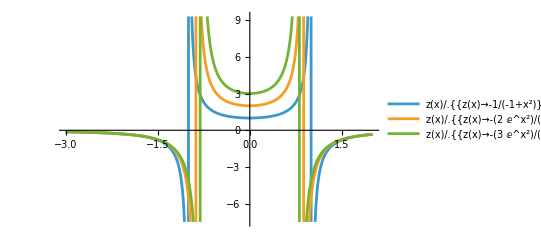

```mathematica
Plot[{z[x]/.sol1, z[x]/.sol2, z[x]/.sol3}, {x,-3,2}, PlotLegends->"Expressions"]
```

4) Rozwiązać równanie liniowe 2 rzędu:

```mathematica
DSolve[z''[x]-4*z'[x]+4*z[x]==x^2, z[x],x]
```

{{z[x]→1/8 (3+4 x+2 x^2)+ⅇ^(2 x) C[1]+ⅇ^(2 x) x C[2]}}

```mathematica
Plot3D[1/8 (3+4 x+2 x^2)+ⅇ^(2 x)+ⅇ^(2 x) x, {x,-3,3}, {y, -2,2}]
```

-Graphics3D-